{Λc 1/2+ 2.287}

{2.26957,4.86221,{3.07849,2.95317,2.47977,2.04279}}

{0.603054}

{{0.18703},{0.177153}}

{Σc 1/2+ 2.454}

{2.41129,4.818,{3.07791,2.95157,2.47714,2.04279}}

{0.915314,0.597787,0.350856}

{{0.804105,0.15433,-0.495445},{0.761641,0.14618,-0.469281}}

{Σc^* 3/2+ 2.518}

{2.51166,5.00767,{3.0803,2.95822,2.48829,2.04279}}

{0.950734,0.620381,0.366263}

{{1.53851,0.525479,-0.487553},{1.45726,0.497728,-0.461806}}

{D 0- 1.867}

{1.83518,3.6295,{3.05738,2.89647,2.39953,2.04279}}

{0.456031,0.254336,0.254336,0.456031}

{D^* 1- 2.009}

{2.00872,4.08918,{3.06671,2.92104,2.43123,2.04279}}

{0.510908,0.291649,0.291649,0.510908}

{{0.457559,-0.369665,0.369665,-0.457559},{0.433395,-0.350143,0.350143,-0.433395}}

{Λb 1/2+ 5.620}

{5.64823,4.59725,{3.07489,2.94322,2.46376,2.04279}}

{0.254015}

{{-0.0323579},{-0.0306491}}

{Σb 1/2+ 5.813}

{5.83455,4.63682,{3.07545,2.94477,2.46619,2.04279}}

{0.714611,0.25627,0.615889}

{{0.844575,0.219235,-0.406106},{0.799974,0.207657,-0.384659}}

{Σb^* 3/2+ 5.833}

{5.87225,4.72773,{3.07671,2.94824,2.47172,2.04279}}

{0.728677,0.261451,0.627899}

{{1.24282,0.286423,-0.669977},{1.17719,0.271297,-0.634596}}

{B 0- 5.280}

{5.24831,3.1413,{3.04458,2.86402,2.36327,2.04279}}

{0.418344,0.17095,0.418344}

{B^* 1- 5.325}

{5.32522,3.47496,{3.05371,2.88701,2.38836,2.04279}}

{0.462412,0.190005,0.190005,0.462412}

{{0.500748,-0.202223,0.202223,-0.500748},{0.474303,-0.191544,0.191544,-0.474303}}

{Mass Spectrum}

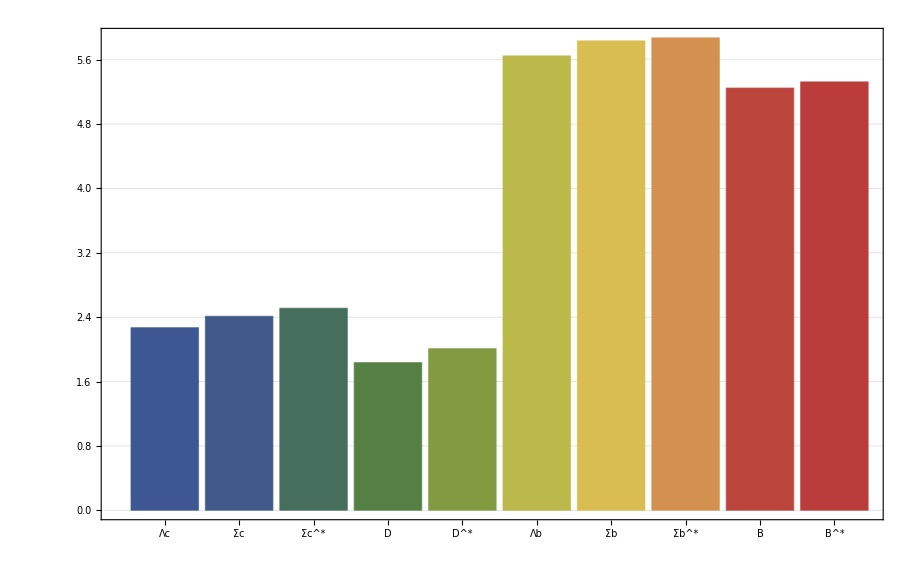

{My Error}

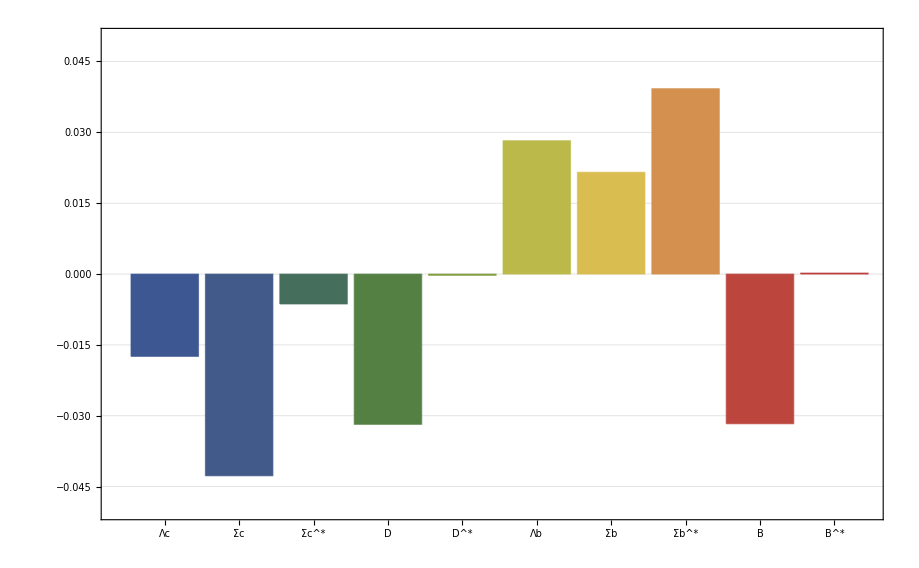

{Charge Radius}

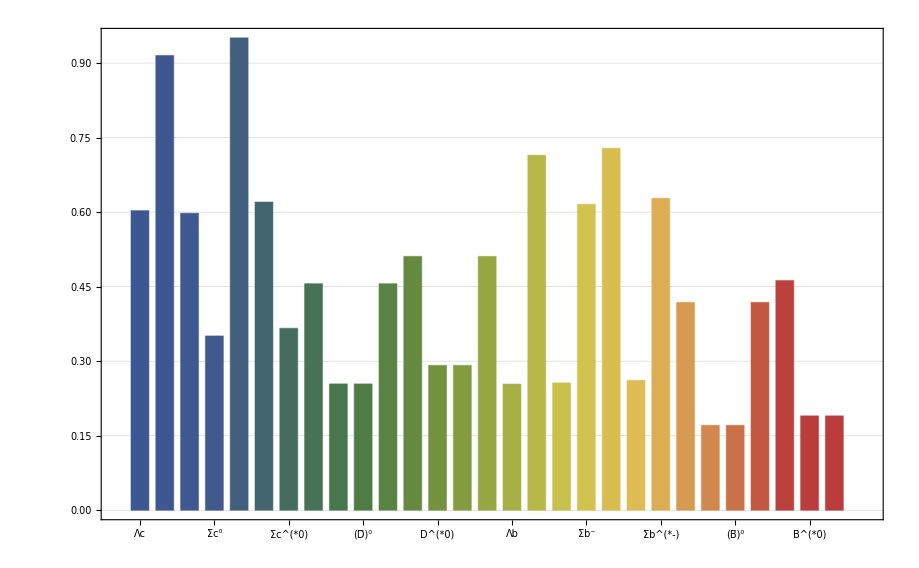

{Magnetic Moment}

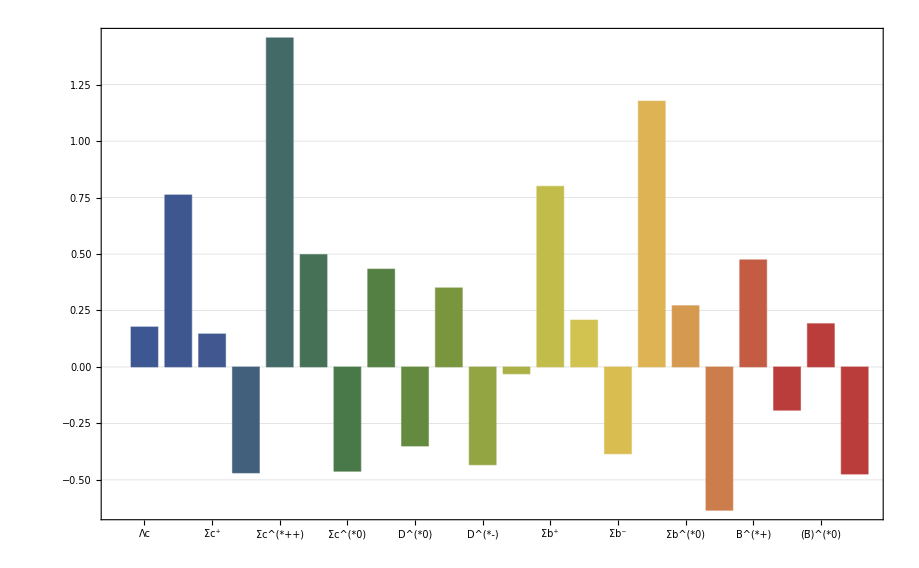

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Λc 1/2+ 2.287"}
Λc=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛc=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},Λc];
μΛc=MagneticMoment[{0,1,0,0,0},{0,0,0,0,0},Λc];
{rΛc}
{{μΛc},{μΛc/μNp}}

{"Σc 1/2+ 2.454"}
Σc=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,32/3},{0,0,0,0},{0,0,0,-8/3}},0]
rΣcpp=ChargeRadius[{0,1,0,2,0},{0,0,0,0,0},Σc];
rΣcp=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},Σc];
rΣc0=ChargeRadius[{0,1,0,0,2},{0,0,0,0,0},Σc];
μΣcpp=MagneticMoment[{0,-1/3,0,4/3,0},{0,0,0,0,0},Σc];μΣcp=MagneticMoment[{0,-1/3,0,2/3,2/3},{0,0,0,0,0},Σc];μΣc0=MagneticMoment[{0,-1/3,0,0,4/3},{0,0,0,0,0},Σc];
{rΣcpp,rΣcp,rΣc0}
{{μΣcpp,μΣcp,μΣc0},{μΣcpp/μNp,μΣcp/μNp,μΣc0/μNp}}

{"Σc^* 3/2+ 2.518"}
ΣcStar=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,-16/3},{0,0,0,0},{0,0,0,-8/3}},0]
rΣcppStar=ChargeRadius[{0,1,0,2,0},{0,0,0,0,0},ΣcStar];
rΣcpStar=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},ΣcStar];
rΣc0Star=ChargeRadius[{0,1,0,0,2},{0,0,0,0,0},ΣcStar];
μΣcppStar=MagneticMoment[{0,1,0,2,0},{0,0,0,0,0},ΣcStar];
μΣcpStar=MagneticMoment[{0,1,0,1,1},{0,0,0,0,0},ΣcStar];
μΣc0Star=MagneticMoment[{0,1,0,0,2},{0,0,0,0,0},ΣcStar];
{rΣcppStar,rΣcpStar,rΣc0Star}
{{μΣcppStar,μΣcpStar,μΣc0Star},{μΣcppStar/μNp,μΣcpStar/μNp,μΣc0Star/μNp}}

{"D 0- 1.867"}
Dq=Hadron[{0,1,0,1},{{0,0,0,0},{0,0,0,16},{0,0,0,0},{0,0,0,0}},0]
rDp=ChargeRadius[{0,1,0,0,0},{0,0,0,0,1},Dq];
rD0=ChargeRadius[{0,1,0,0,0},{0,0,0,1,0},Dq];
rD0bar=ChargeRadius[{0,0,0,1,0},{0,1,0,0,0},Dq];
rDm=ChargeRadius[{0,0,0,0,1},{0,1,0,0,0},Dq];
{rDp,rD0,rD0bar,rDm}

{"D^* 1- 2.009"}
DqStar=Hadron[{0,1,0,1},{{0,0,0,0},{0,0,0,-16/3},{0,0,0,0},{0,0,0,0}},0]
rDpStar=ChargeRadius[{0,1,0,0,0},{0,0,0,0,1},DqStar];
rD0Star=ChargeRadius[{0,1,0,0,0},{0,0,0,1,0},DqStar];
rD0barStar=ChargeRadius[{0,0,0,1,0},{0,1,0,0,0},DqStar];
rDmStar=ChargeRadius[{0,0,0,0,1},{0,1,0,0,0},DqStar];
μDpStar=MagneticMoment[{0,1,0,0,0},{0,0,0,0,1},DqStar];
μD0Star=MagneticMoment[{0,1,0,0,0},{0,0,0,1,0},DqStar];
μD0barStar=MagneticMoment[{0,0,0,1,0},{0,1,0,0,0},DqStar];
μDmStar=MagneticMoment[{0,0,0,0,1},{0,1,0,0,0},DqStar];
{rDpStar,rD0Star,rD0barStar,rDmStar}
{{μDpStar,μD0Star,μD0barStar,μDmStar},{μDpStar/μNp,μD0Star/μNp,μD0barStar/μNp,μDmStar/μNp}}

{"Λb 1/2+ 5.620"}
Λb=Hadron[{1,0,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛb=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},Λb];
μΛb=MagneticMoment[{1,0,0,0,0},{0,0,0,0,0},Λb];
{rΛb}
{{μΛb},{μΛb/μNp}}

{"Σb 1/2+ 5.813"}
Σb=Hadron[{1,0,0,2},{{0,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,-8/3}},0]
rΣbp=ChargeRadius[{1,0,0,2,0},{0,0,0,0,0},Σb];
rΣb0=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},Σb];
rΣbm=ChargeRadius[{1,0,0,0,2},{0,0,0,0,0},Σb];
μΣbp=MagneticMoment[{-1/3,0,0,4/3,0},{0,0,0,0,0},Σb];μΣb0=MagneticMoment[{-1/3,0,0,2/3,2/3},{0,0,0,0,0},Σb];μΣbm=MagneticMoment[{-1/3,0,0,0,4/3},{0,0,0,0,0},Σb];
{rΣbp,rΣb0,rΣbm}
{{μΣbp,μΣb0,μΣbm},{μΣbp/μNp,μΣb0/μNp,μΣbm/μNp}}

{"Σb^* 3/2+ 5.833"}
ΣbStar=Hadron[{1,0,0,2},{{0,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,-8/3}},0]
rΣbpStar=ChargeRadius[{1,0,0,2,0},{0,0,0,0,0},ΣbStar];
rΣb0Star=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},ΣbStar];
rΣbmStar=ChargeRadius[{1,0,0,0,2},{0,0,0,0,0},ΣbStar];
μΣbpStar=MagneticMoment[{1,0,0,2,0},{0,0,0,0,0},ΣbStar];
μΣb0Star=MagneticMoment[{1,0,0,1,1},{0,0,0,0,0},ΣbStar];
μΣbmStar=MagneticMoment[{1,0,0,0,2},{0,0,0,0,0},ΣbStar];
{rΣbpStar,rΣb0Star,rΣbmStar}
{{μΣbpStar,μΣb0Star,μΣbmStar},{μΣbpStar/μNp,μΣb0Star/μNp,μΣbmStar/μNp}}

{"B 0- 5.280"}
Bq=Hadron[{1,0,0,1},{{0,0,0,16},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]
rBp=ChargeRadius[{0,0,0,1,0},{1,0,0,0,0},Bq];
rB0=ChargeRadius[{0,0,0,0,1},{1,0,0,0,0},Bq];
rB0bar=ChargeRadius[{1,0,0,0,0},{0,0,0,0,1},Bq];
rBm=ChargeRadius[{1,0,0,0,0},{0,0,0,1,0},Bq];
{rBp,rB0,rBm}

{"B^* 1- 5.325"}
BqStar=Hadron[{1,0,0,1},{{0,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]
rBpStar=ChargeRadius[{0,0,0,1,0},{1,0,0,0,0},BqStar];
rB0Star=ChargeRadius[{0,0,0,0,1},{1,0,0,0,0},BqStar];
rB0barStar=ChargeRadius[{1,0,0,0,0},{0,0,0,0,1},BqStar];
rBmStar=ChargeRadius[{1,0,0,0,0},{0,0,0,1,0},BqStar];
μBpStar=MagneticMoment[{0,0,0,1,0},{1,0,0,0,0},BqStar];
μB0Star=MagneticMoment[{0,0,0,0,1},{1,0,0,0,0},BqStar];
μB0barStar=MagneticMoment[{1,0,0,0,0},{0,0,0,0,1},BqStar];
μBmStar=MagneticMoment[{1,0,0,0,0},{0,0,0,1,0},BqStar];
{rBpStar,rB0Star,rB0barStar,rBmStar}
{{μBpStar,μB0Star,μB0barStar,μBmStar},{μBpStar/μNp,μB0Star/μNp,μB0barStar/μNp,μBmStar/μNp}}

{"Mass Spectrum"}
BarChart[{First[Λc],First[Σc],First[ΣcStar],First[Dq],First[DqStar],First[Λb],First[Σb],First[ΣbStar],First[Bq],First[BqStar]},Frame->True,ChartLabels->{"Λc","Σc","Σc^*","D","D^*","Λb","Σb","Σb^*","B","B^*"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{
(First[Λc]-2.287),
(First[Σc]-2.454),
(First[ΣcStar]-2.518),
(First[Dq]-1.867),
(First[DqStar]-2.009),
(First[Λb]-5.620),
(First[Σb]-5.813),
(First[ΣbStar]-5.833),
(First[Bq]-5.280),
(First[BqStar]-5.325)},Frame->True,ChartLabels->{"Λc","Σc","Σc^*","D","D^*","Λb","Σb","Σb^*","B","B^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.05},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΛc,rΣcpp,rΣcp,rΣc0,rΣcppStar,rΣcpStar,rΣc0Star,rDp,rD0,rD0bar,rDm,rDpStar,rD0Star,rD0barStar,rDmStar,rΛb,rΣbp,rΣb0,rΣbm,rΣbpStar,rΣb0Star,rΣbmStar,rBp,rB0,rB0bar,rBm,rBpStar,rB0Star,rB0barStar,SuperStar[rBm]},Frame->True,ChartLabels->{"Λc","Σc^(++)","Σc^+","Σc^0","Σc^(*++)","Σc^(*+)","Σc^(*0)","D^+","D^0","(D̄)^0","D^-","D^(*+)","D^(*0)","(D̄)^(*0)","D^(*-)","Λb","Σb^+","Σb^0","Σb^-","Σb^(*+)","Σb^(*0)","Σb^(*-)","B^+","B^0","(B̄)^0","B^-","B^(*+)","B^(*0)","(B̄)^(*0)","B^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΛc/μNp,μΣcpp/μNp,μΣcp/μNp,μΣc0/μNp,μΣcppStar/μNp,μΣcpStar/μNp,μΣc0Star/μNp,μDpStar/μNp,μD0Star/μNp,μD0barStar/μNp,μDmStar/μNp,μΛb/μNp,μΣbp/μNp,μΣb0/μNp,μΣbm/μNp,μΣbpStar/μNp,μΣb0Star/μNp,μΣbmStar/μNp,μBpStar/μNp,μB0Star/μNp,μB0barStar/μNp,μBmStar/μNp},Frame->True,ChartLabels->{"Λc","Σc^(++)","Σc^+","Σc^0","Σc^(*++)","Σc^(*+)","Σc^(*0)","D^(*+)","D^(*0)","(D̄)^(*0)","D^(*-)","Λb","Σb^+","Σb^0","Σb^-","Σb^(*+)","Σb^(*0)","Σb^(*-)","B^(*+)","B^(*0)","(B̄)^(*0)","B^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```